## Step-Growth Polymerization

Note: Functions specialized to explicitly disallow self-loops

Much faster & arguably physical

Dynamic Version

```mathematica
SeedRandom[1];
boxSize=35;
listOfPositions=randomPackingMonomerConfiguration[boxSize,2];
```

```mathematica
Dynamic[Graphics[{
chainGraphic/@listOfPositions,
{EdgeForm[Directive[Dashed,Black]],FaceForm[None],Rectangle[{-boxSize,-boxSize}/2,{boxSize,boxSize}/2]}
},PlotRange->All,ImageSize->500,PlotRangePadding->1]]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,0.1,0.1,boxSize],
{100000}]
]
```

$Aborted

NestWhileList

```mathematica
SeedRandom[1];
boxSize=35;
listOfPositions=randomPackingMonomerConfiguration[boxSize,2];

positions=QuietEcho[nestWhileListWithMonitor[moveAllChains[#,0.1,0.1,boxSize]&,listOfPositions,50000,Length[#]>1&]];
cleanPositions=DeleteDuplicates[positions];
movie=collisionEventFrames[cleanPositions,boxSize];
```

```mathematica
{{mn,mnRxn},{mw,mwRxn}}=numberAndWeightFractions[cleanPositions];
```

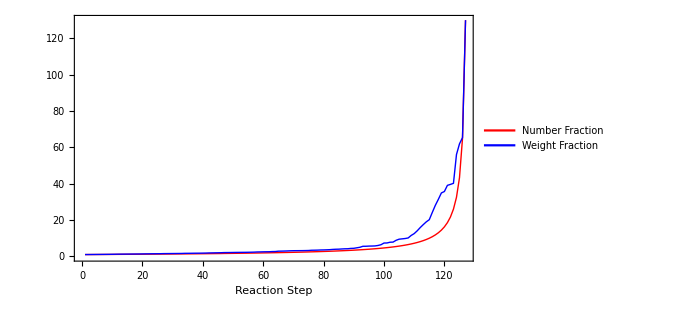

```mathematica
ListLinePlot[{mnRxn,mwRxn},Frame->True,FrameLabel->{"Reaction Step",None},ImageSize->500,LabelStyle->Directive[Black,Thick,18],PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},PlotRange->All,PlotLegends->Placed[LineLegend[Automatic,{"Number Fraction","Weight Fraction"}],{0.25,0.75}]]
```

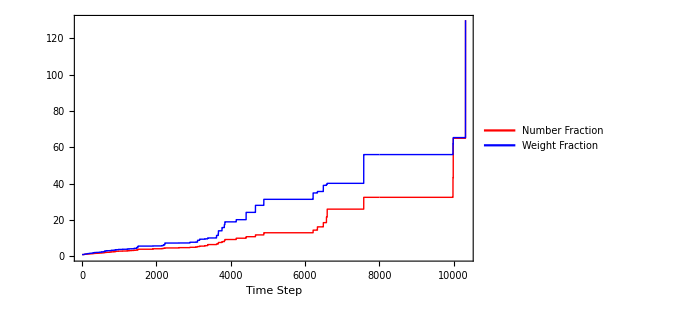

```mathematica
ListLinePlot[{mn,mw},Frame->True,FrameLabel->{"Time Step",None},ImageSize->500,LabelStyle->Directive[Black,Thick,18],PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},PlotRange->All,PlotLegends->Placed[LineLegend[Automatic,{"Number Fraction","Weight Fraction"}],{0.25,0.75}]]
```

```mathematica
Export["step-growth-polymerization__no-self-loops__140-monomers__events.gif",movie]
```

step-growth-polymerization__no-self-loops__140-monomers__events.gif

## Initialization Functions

### Visualization

```mathematica
chainGraphic[positions_]:= {
{Circle[#,1/2]&/@positions[[2;;-2]]},
{Disk[#,1/2]&/@positions[[{1,-1}]]}
}

chainGraphic[positions:{{x_,y_}}]:= {
{LightGray,Disk[{x,y},1/2]}
}

chainGraphicsWithClock[listOfPositions_,iteration_,boxSize_]:=With[{clock=ClockGauge[DatePlus[{2000,1,1,0,0,0},{iteration-1,"Second"}],PlotTheme->"Minimal"]},
{chainGraphic/@listOfPositions,Inset[clock,{0,-boxSize/2},{0,1},Scaled[0.25]]}]

returnCollisionEventIndices[listOfPositions_]:=Most[Accumulate[Prepend[Length/@Split[Length/@listOfPositions],1]]]

monomersPerChain[listOfPositions_]:=Map[Length,listOfPositions,{2}]

numberAndWeightFractions[listOfPositions_]:=Block[{
monomers=monomersPerChain[listOfPositions],
indices=returnCollisionEventIndices[listOfPositions],
mn,mw},
mn=N[(#2.#1)/Total[#2]]&@@Transpose[Tally[#]]&/@monomers;
mw=N[(#2.#1^2)/(#2.#1)]&@@Transpose[Tally[#]]&/@monomers;
{
{mn,mn[[indices]]},
{mw,mw[[indices]]}
}
]

collisionEventFrames[listOfPositions_,boxSize_,imageSize_:350]:=With[{indices=returnCollisionEventIndices[listOfPositions]},
Table[Graphics[{
chainGraphicsWithClock[listOfPositions[[i]],i,boxSize]
},PlotRange->{{-boxSize,boxSize}/2,{-3/4 boxSize,boxSize/2}},ImageSize->imageSize],{i,indices}]
]
```

```mathematica
nestListWithMonitor[f_,init_,n_]:=Module[{it=0},
PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]

nestWhileListWithMonitor[f_,init_,n_,test_,m_:1]:=Module[{it=0},
PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestWhileList[(it++;f[#])&,init,test,m,n]]
```

### Correlated Polymer Microstructures

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]<bondLength

angularRange[correlation_]:={-1,1}(1-correlation)2π/3

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->"Distance"],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]

randomDimer[origin_]:=Join[{origin},{AngleVector[origin,RandomReal[2π]]}]

hexagonalDimerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}},
latticeCoords=Tuples[linearSpacingFactor Range[-size,size,3],2],sites,cleanSize=size-3},
sites=Select[latticeCoords.hexagonalLatticeVectors,cleanSize/2>#[[1]]>-cleanSize/2&&cleanSize/2>#[[2]]>-cleanSize/2&];
randomDimer/@sites
]

randomPackingDimerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
proc=HardcorePointProcess[1,3 linearSpacingFactor,2],sites,cleanSize=size-3},
sites=RandomPointConfiguration[proc,Rectangle[{-cleanSize/2,-cleanSize/2},{cleanSize/2,cleanSize/2}]]["Points"];
randomDimer/@sites
]

randomPackingMonomerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
proc=HardcorePointProcess[1, linearSpacingFactor,2],sites,cleanSize=size-1},
sites=RandomPointConfiguration[proc,Rectangle[{-cleanSize/2,-cleanSize/2},{cleanSize/2,cleanSize/2}]]["Points"];
List/@sites
]
```

### Single Chain Reptation

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]

displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];

newPositions/@Range[Length[Δ]]
]
```

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]

moveSingleChain[positions_,ds_,stickiness_,size_]:= 
Block[{newPositions,cleanSize=size-1},

newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];

If[Max[Abs[MinMax[newPositions]]]>cleanSize/2,Return[positions]];

If[collisionFreeQ[newPositions],newPositions,positions]

]
```

### Multiple Chain Reptation

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

horizontalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)
verticalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(yMaxA>yMinB&&yMinA<yMaxB)

connectivityMatrixIndexHorizontal[bbs_,{i_,j_}]:=horizontalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]
connectivityMatrixIndexVertical[bbs_,{i_,j_}]:=verticalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],pruneHorizontally},
pruneHorizontally=Select[s,connectivityMatrixIndexHorizontal[bbs,#]&];
SparseArray[pruneHorizontally->(connectivityMatrixIndexVertical[bbs,#]&/@pruneHorizontally),{l,l}]
]

returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[Thread[{pos,Range[Length[pos]]}],xMax>#[[1,1]]>xMin&&yMax>#[[1,2]]>yMin&],{pos,{positionsA,positionsB}}]
]

returnAllCollisions[posA_,posB_]:=Block[{nf,sorted,
posShortcoords,posShortIndices,
posLongcoords,posLongIndices,
cols},

sorted=SortBy[{posA,posB},Length];
posShortcoords=sorted[[1,All,1]];posShortIndices=sorted[[1,All,2]];
posLongcoords=sorted[[2,All,1]];posLongIndices=sorted[[2,All,2]];

nf=Nearest[posLongcoords->{"Index","Distance"}];
cols=Select[Prepend[First[nf[posShortcoords[[#]]]],#]&/@Range[Length[posShortcoords]],#[[3]]<1&];

{posLongIndices[[#2]],posShortIndices[[#1]],#3}&@@@cols

]

pairwiseChainCollisions[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,{},returnAllCollisions[posA,posB]]
]
```

```mathematica
compareEndPoints[listOfPositions_,{i_,j_}]:=
Block[{
endsI=listOfPositions[[i,{1,-1}]],
endsJ=listOfPositions[[j,{1,-1}]],
vecs},

vecs=Tuples[{endsI,endsJ}];
Thread[SquaredEuclideanDistance@@@vecs<1]
]

(*mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,{{i},{j}}->Join[Reverse[posI],posJ]],
{False,True,_,_},ReplacePart[listOfPositions,{{i},{j}}->Join[posJ,posI]],
{False,False,True,_},ReplacePart[listOfPositions,{{i},{j}}->Join[posI,posJ]],
{False,False,False,True},ReplacePart[listOfPositions,{{i},{j}}->Join[posI,Reverse[posJ]]],
_,listOfPositions
]
]*)

mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{Reverse[posI],posJ}]],
{False,True,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posJ,posI}]],
{False,False,True,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,posJ}]],
{False,False,False,True},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,Reverse[posJ]}]],
_,listOfPositions
]
]

collisionFreeFurtherQ[positions_]:=With[{nf=Nearest[positions->All],l=Length[positions]},
Length[Join@@Table[Select[nf[positions[[i]],{All,1}],Abs[#Index-i]>1&],{i,l}]]==0]

checkProposedMerger[{i_,j_},{posI_,posJ_}]:=
With[{proposal=Join[posI,posJ]},
If[collisionFreeFurtherQ[proposal],{{i},{j}}->proposal,Echo["Intersecting Merger"];{}]
]
```

```mathematica
checkForCollisions[{listOfPositions_,oldListOfPositions_}]:=Catch[
Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks,lengths},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[listOfPos]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisions[{listOfPos,bbs},#]&/@nonzero;
If[Length[Join@@collisions]==0,Echo["No Collisions"];Return[listOfPos]];

lengths=Sort[Length/@Extract[listOfPos,List/@#]]&/@nonzero;

Do[
If[
Length[collisions[[a]]]>0&&
(1<collisions[[a,j,1]]<lengths[[a,1]]||
1<collisions[[a,j,2]]<lengths[[a,2]]),
Echo["No-terminating collisions"];Throw[oldListOfPositions]],{a,Length[collisions]},{j,Length[collisions[[a]]]}];

collisionIndices= Extract[nonzero,Position[collisions,Except[{}],1,Heads->False]];
endpointChecks=compareEndPoints[listOfPos,#]&/@collisionIndices;
If[Nor@@Flatten[endpointChecks],Echo["No Mergers"];Return[oldListOfPositions]];

Do[
listOfPos=mergeEndPoints[listOfPos,collisionIndices[[a]],endpointChecks[[a]]],
{a,Length[collisionIndices]}
];

DeleteDuplicates[listOfPos]
]
]

moveAllChains[listOfPositions_,ds_,stickiness_,size_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds,stickiness,size]&/@listOfPos;
checkForCollisions[{listOfPos,listOfPositions}]
]
```